```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
mub={0,50,100,150,200,250,300,350,400,450,475,500,530};
fitdata=Table[Import["./mub"<>ToString[mub[[i]]]<>"data.dat"],{i,1,Length[mub]}];
```

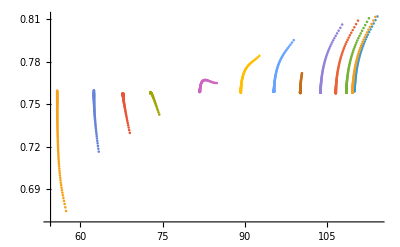

```mathematica
ListPlot[fitdata,PlotRange->All]
```

```mathematica
fitfun=Table[Interpolation[fitdata[[i]]],{i,1,Length[mub]}];
```

```mathematica
T=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-0.759)/0.759]==0.01,{x,fitdata[[i]][[-10]][[1]],fitdata[[i]][[1]][[1]],fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["nu0p01.dat",%];
```

FindRoot::reged: 点 {110.019} 位于搜索区域 {110.019,114.2} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {108.515} 位于搜索区域 {108.515,112.639} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {106.593} 位于搜索区域 {106.593,110.643} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

General::stop: 在本次计算中，FindRoot::reged 的进一步输出将被抑制.

{110.019,109.767,108.515,106.593,103.817,100.232,95.2972,89.4463,83.3555,73.5964,67.9176,62.4473,55.7501}

```mathematica
T=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-0.759)/0.759]==0.02,{x,fitdata[[i]][[-7]][[1]],fitdata[[i]][[1]][[1]],fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["nu0p02.dat",%];
```

FindRoot::reged: 点 {110.019} 位于搜索区域 {110.019,114.2} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {108.515} 位于搜索区域 {108.515,112.639} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {106.593} 位于搜索区域 {106.593,110.643} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

General::stop: 在本次计算中，FindRoot::reged 的进一步输出将被抑制.

InterpolatingFunction::dmval: 输入值 {100.43} 位于插值函数的数据范围之外. 将使用外推法.

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

{110.019,110.024,108.515,106.593,103.817,100.43,95.8211,90.059,82.7624,74.2746,68.2646,62.5638,55.7501}

```mathematica
T=Table[Flatten[FindRoot[Abs[(fitfun[[i]][x]-0.759)/0.759]==0.03,{x,fitdata[[i]][[-10]][[1]],fitdata[[i]][[1]][[1]],fitdata[[i]][[-1]][[1]]}],2][[1]][[2]],{i,1,Length[mub]}]
Export["nu0p03.dat",%];
```

InterpolatingFunction::dmval: 输入值 {100.43} 位于插值函数的数据范围之外. 将使用外推法.

FindRoot::reged: 点 {100.43} 位于搜索区域 {100.096,100.43} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::lstol: 线搜索把步长降低到由 AccuracyGoal 和 PrecisionGoal 指定的容差范围内，但是无法使优化目标函数的值减小得足够多. 您可能需要多于 MachinePrecision 位的工作精度以满足这些容差.

InterpolatingFunction::dmval: 输入值 {74.3777} 位于插值函数的数据范围之外. 将使用外推法.

FindRoot::reged: 点 {74.3777} 位于搜索区域 {72.7665,74.3777} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

FindRoot::reged: 点 {55.7501} 位于搜索区域 {55.7501,57.3672} 的边上坐标为 1 的位置处，并且计算搜索方向指向区域外.

General::stop: 在本次计算中，FindRoot::reged 的进一步输出将被抑制.

{110.804,110.435,109.318,107.422,104.697,100.43,96.5423,91.931,82.7624,74.3777,68.6457,62.7183,55.7501}

```mathematica
Export["mub.dat",mub]
```

mub.dat

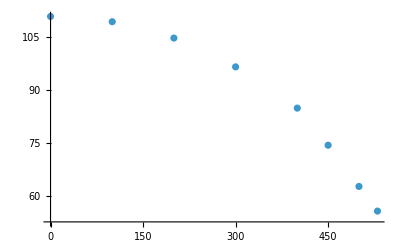

```mathematica
ListPlot[Transpose[{mub,T}],PlotRange->All]
```